```mathematica
ClearAll["Global`*"]
```

#### P1

```mathematica
f1[x_,y_]:=x^2+y^2-4x-2y+7
cts1[x_,y_]:={x>=0,y>=0,x+y<=5}
```

```mathematica
(* Absolute Min *) Minimize[{f1[x,y]}~Join~cts1[x,y],{x,y}]
```

{2,{x→2,y→1}}

```mathematica
(* Absolute Max *) Maximize[{f1[x,y]}~Join~cts1[x,y],{x,y}]
```

{22,{x→0,y→5}}

#### P2

```mathematica
cts2=Eliminate[{x==2t,y==t+1},t]
```

2 (-1+y)==x

```mathematica
(* Min: Exists *) Minimize[{x y,cts2},{x,y}]
```

{-1/2,{x→-1,y→1/2}}

```mathematica
(* Max: Not Exist *) Maximize[{x y,cts2},{x,y}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{x→Indeterminate,y→Indeterminate}}

#### P3

```mathematica
f3[x_,y_]:=x^2-4x+y^2+9;
cts3[x_,y_]:=4x^2+9y^2==36;
```

```mathematica
(* Min *) mi=Minimize[{f3[x,y],cts3[x,y]},{x,y}]
```

{6,{x→3,y→0}}

```mathematica
(* Max *) mx=Maximize[{f3[x,y],cts3[x,y]},{x,y}]
```

{30,{x→-3,y→0}}

```mathematica
min=mi[[2,All,2]]
max=mx[[2,All,2]]
```

{3,0}

{-3,0}

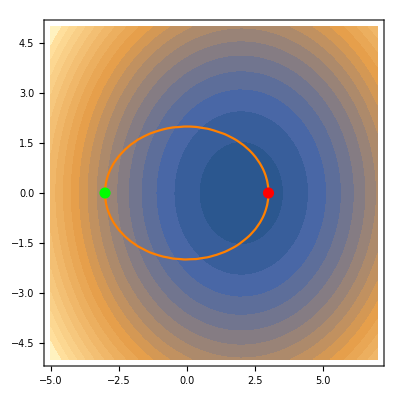

```mathematica
Show[
ContourPlot[f3[x,y],{x,-5,7},{y,-5,5},Contours->20,ContourStyle->None,Epilog->{PointSize[0.02],Red,Point[{min}],Green, Point[{max}]}],
ContourPlot[4 x^2+9 y^2==36,{x,-5,7},{y,-5,5},ColorFunction->(Orange&)]
]
```

#### P4

```mathematica
Maximize[{x y z,36x^2+9y^2+4z^2==36},{x,y,z},PositiveReals]//Simplify
```

{2/(√3),{x→2/(√3 Root1.15Root[{-4+3 #1^2&,-8 #1-12 #2+3 #2^3&},{1,3}]1.1547005383792515 Root1.73Root[{-4+3 #1^2&,-8 #1-12 #2+3 #2^3&,48-36 #2^2 #3^2+9 #2^4 #3^2+4 #2^2 #3^4&},{1,3,4}]1.7320508075688772),y→Root1.15Root[{-4+3 #1^2&,-8 #1-12 #2+3 #2^3&},{1,3}]1.1547005383792515,z→Root1.73Root[{-4+3 #1^2&,-8 #1-12 #2+3 #2^3&,48-36 #2^2 #3^2+9 #2^4 #3^2+4 #2^2 #3^4&},{1,3,4}]1.7320508075688772}}

```mathematica
%//N
```

{1.1547,{x→0.57735,y→1.1547,z→1.73205}}

```mathematica
Minimize[{18/100 a b+16/100 2b c+12/100 2a c,a b c ==16},{a,b,c},PositiveReals]//N
```

{4.57172,{a→3.35979,b→2.51984,c→1.88988}}

```mathematica
(* With Maple *)
```